## Import Utils

```mathematica
Get["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

```mathematica
(*NotebookEvaluate["D:\\Documents\\workspace\\课题\\PN_inverse\\InversePNUtils.nb"]*)
```

```mathematica
NotebookEvaluate["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"]
```

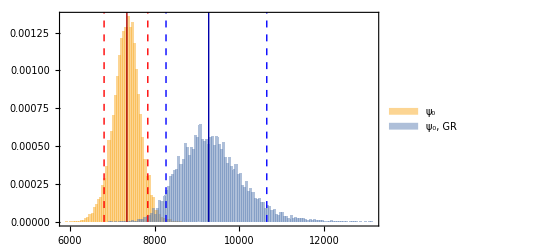

```mathematica
PlotComparisonBetween[samples["cpsi0"]["cpsi0"],samples["cpsi0"]["psi0"],Range[10,100,1],0,BCI["cpsi0"]["spin1z"][[1]],BCI["cpsi0"]["spin2z"][[1]]]
```

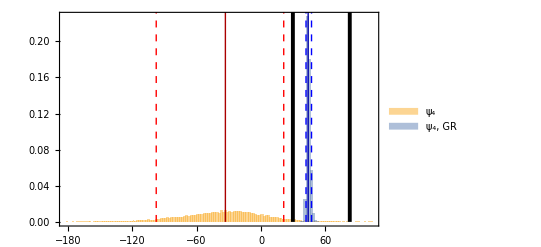

```mathematica
PlotComparisonBetween[samples["cpsi4"]["cpsi4"],samples["cpsi4"]["psi4"],Range[10,100,1],4,BCI["cpsi4"]["spin1z"][[1]],BCI["cpsi4"]["spin2z"][[1]]]
```

```mathematica
ResourceFunction["MaTeXInstall"][]
```

PacletObject[…]

```mathematica
<<MaTeX`
```

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

## 设置non-GR参数字符flag Gw@150914!

```mathematica
eventID="GW150914_095045";

deviationType="cpsi";
deviationOrders=List[0,2,3,4,"5l",6,"6l"];
deviationNames=List["cpsi0","cpsi2","cpsi3","cpsi4","cpsi5l","cpsi6","cpsi6l"];
psiNames=List["psi0","psi2","psi3","psi4","psi5l","psi6","psi6l"];
```

```mathematica
"alpha3"
```

alpha3

```mathematica
"3, 4, 5l, 6; 0, 2, 6l"
```

3, 4, 6, 7, 5l; 0, 2, 6l

## Prepare Data from CSV or HDF

```mathematica
csvPath="D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv"<>"\\"<>eventID;
csvNames=eventID<>"_"<>#<>".csv"& /@ deviationNames;

csvFilePaths=csvPath<>"\\"<>#& /@ csvNames;
```

### from CSV

```mathematica
samples=<||>;
Do[
CSVSamples=Import["D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv\\GW150914_095045\\GW150914_095045_"<>n<>".csv"];
samples[n]=<||>;
samples[n]["mass1"]=CSVSamples[[All,1]][[2;;]];
samples[n]["mass2"]=CSVSamples[[All,2]][[2;;]];
samples[n]["spin1z"]=CSVSamples[[All,3]][[2;;]];
samples[n]["spin2z"]=CSVSamples[[All,4]][[2;;]];
samples[n]["eta"]=CSVSamples[[All,5]][[2;;]];
samples[n]["Mchirp"]=CSVSamples[[All,6]][[2;;]];
samples[n][n]=CSVSamples[[All,7]][[2;;]];
samples[n]["chis"]=χs[samples["spin1z"],samples["spin2z"]];
samples[n]["chia"]=χa[samples["spin1z"],samples["spin2z"]];,
{n,deviationNames}
]
```

```mathematica
samples["cpsi4"]["mass1"]
```

### Calculate GR Coefficients

```mathematica
Do[
samples[deviationNames[[n]]][psiNames[[n]]]=MapThread[
Psi[deviationOrders[[n]],η[#1,#2],M[#1,#2],#3,#4]&,
{samples[deviationNames[[n]]]["mass1"],samples[deviationNames[[n]]]["mass2"],samples[deviationNames[[n]]]["spin1z"],samples[deviationNames[[n]]]["spin2z"]}
];,
{n,Range[Length[deviationOrders]]}
]
```

## Calculate BCIs

```mathematica
BCI=<||>;
Do[
BCI[deviationNames[[n]]]=<||>;
BCI[deviationNames[[n]]]["mass1"]=PlotParameterWithBCI[samples[deviationNames[[n]]]["mass1"],Subscript["m","1"]][[1]];
BCI[deviationNames[[n]]]["mass2"]=PlotParameterWithBCI[samples[deviationNames[[n]]]["mass2"],Subscript["m","2"]][[1]];
BCI[deviationNames[[n]]]["spin1z"]=PlotParameterWithBCI[samples[deviationNames[[n]]]["spin1z"],"spin1z"][[1]];
BCI[deviationNames[[n]]]["spin2z"]=PlotParameterWithBCI[samples[deviationNames[[n]]]["spin2z"],"spin2z"][[1]];
BCI[deviationNames[[n]]][deviationNames[[n]]]=PlotParameterWithBCI[samples[deviationNames[[n]]][deviationNames[[n]]],deviationNames[[n]]][[1]];
BCI[deviationNames[[n]]][psiNames[[n]]]=PlotParameterWithBCI[samples[deviationNames[[n]]][psiNames[[n]]],psiNames[[n]]][[1]];,
{n,Range[Length[deviationOrders]]}
]
```

## Calculate and Plot Points over which Tapes Meet

### Prepare Data Objects

```mathematica
m1s=Range[15,150,1];
m2s=Range[15,150,1];
```

```mathematica
pInterval=<||>;
tapeIntervals=<||>;
tapes=<||>;
plots=<||>;
```

```mathematica
Keys[samples["cpsi0"]]
```

{mass1,mass2,spin1z,spin2z,eta,Mchirp,cpsi0,chis,chia,psi0,psi2,psi3}

### GW150914_095045 IMRPhenomXAS (c)onstant, psi_j -> cpsij: j = 0, 2, 3, 4, 5l, 6, 6l; j = -2, 1, psi1 = psi_{-2} = 0, 反解不了； j = 5, psi5和coa_phase简并； j = 7, 暂时不管；

### Manipulate cpsi0

```mathematica
m1s=Range[15,150,1];
m2s=Range[15,150,1];

n="cpsi0";n1="psi3";n2="psi2";
prob=0.83;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

(*plotedPoints=<||>;*)

Quiet[
(*tapeIntervals["psi3"]=Quantile[samples["cpsi0"]["psi3"],pInterval["cpsi0"]];
tapes[n]["psi3"]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals["psi3"],{m2s},{2},{3,BCI["cpsi0"]["spin1z"][[2]],BCI["cpsi0"]["spin2z"][[2]]},tapeIntervals["mass2"],2];
*)

tapeIntervals[n1]=Quantile[samples[n][n1],pInterval[n]];
tapes[n][n1]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n1],{m2s},{2},
{3,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
(*plotedPoints[n1]=List[];
AppendTo[plotedPoints[n1],Select[tapes[n][n1][[1]],#[[1]]>=#[[2]]&]];
AppendTo[plotedPoints[n1],Select[tapes[n][n1][[2]],#[[1]]>=#[[2]]&]];*)

tapeIntervals[n2]=Quantile[samples[n][n2],pInterval[n]];
tapes[n][n2]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n2],{m2s},{2},
{2,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
(*plotedPoints[n2]=List[];
AppendTo[plotedPoints[n2],Select[tapes[n][n2][[1]],#[[1]]>=#[[2]]&]];
AppendTo[plotedPoints[n2],Select[tapes[n][n2][[2]],#[[1]]>=#[[2]]&]];*)

tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{0,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
(*plotedPoints[n]=List[];
AppendTo[plotedPoints[n],Select[tapes[n][n][[1]],#[[1]]>=#[[2]]&]];
AppendTo[plotedPoints[n],Select[tapes[n][n][[2]],#[[1]]>=#[[2]]&]];*)
];



plots[n]=Legended[ListLinePlot[
{
tapes[n][n1][[1]][[2;;]],
tapes[n][n1][[2]][[2;;]],

tapes[n][n2][[1]][[2;;]],
tapes[n][n2][[2]][[2;;]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]
},
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Filling->{1->{2},3->{4},5->{6}},
FillingStyle->{HatchFilling["Diagonal"]},
AxesLabel->{TraditionalForm[Subscript[m,1]/Subscript[m,"☉"]],TraditionalForm[Subscript[m,2]/Subscript[m,"☉"]]},
AspectRatio->1(*,
(*PlotLegends->{1,2,3,4,5,6,7}*),
PlotRange->{{30,70},{10,30}}*),
Epilog->{
White,Opacity[1],Polygon[{{100,100},{10,100},{10,10} }],
Black,Dashed,Line[{{0,0},{100,100}}],
White,EdgeForm[Gray],Disk[{63.8,21.8},Offset[5]]
(*Black,Disk[{63.8,21.8},Offset[5]]*)
	},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[p==value]]],
ImageSize->Medium
],
Placed[
Column[{LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},
{"GR "<>ToString[TraditionalForm[Subscript[ψ,3]]],"GR "<>ToString[TraditionalForm[Subscript[ψ,2]]],"non-GR "<>ToString[TraditionalForm[Subscript[ψ,0]]],TraditionalForm[Subscript[m,1]==Subscript[m,2]]},LegendLayout->"Column"],PointLegend[{Black},{"Intersection \n point"},LegendMarkers->Graphics[{White,EdgeForm[Gray],Disk[{0,0},Offset[5]]}],LegendMarkerSize->15]}],
{0.78,0.8}]
]
```

-Graphics-

### Manipulate cpsi2

```mathematica
m1s=Range[1,150,3];
m2s=Range[1,150,3];

n="cpsi2";n1="psi0";n2="psi3";
(*prob=0.957;*)
prob=0.902;
(*0.6一个超远点，0.9往后又会远离*)

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{2,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

plots[n]=ListLinePlot[
{tapes[n]["mass1"][[1]][[2;;]],
tapes[n]["mass1"][[2]][[2;;]],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]},
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Filling->{1->{2},3->{4},5->{6}},
FillingStyle->{HatchFilling["Diagonal"]},AxesLabel->{TraditionalForm[Subscript[m,1]/Subscript[m,"☉"]],TraditionalForm[Subscript[m,2]/Subscript[m,"☉"]]},AspectRatio->1,PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},Epilog->{
White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],
Black,Dashed,Line[{{0,0},{100,100}}],
(*最后绘制图例-优先级最高*)Inset[
Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{"GR ",Subscript[ψ,0]}]],
TraditionalForm[Row[{"GR ",Subscript[ψ,3]}]],
TraditionalForm[Row[{"non-GR ",Subscript[ψ,2]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left],
Background->White],Scaled[{0.3,0.8}],{0,0}]},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[p==value]]],
ImageSize->Medium]
```

-Graphics-

```mathematica
plots[n]=ListLinePlot[
{tapes[n][n1][[1]][[2;;]],
tapes[n][n1][[2]][[2;;]],
tapes[n][n2][[1]][[2;;]],
tapes[n][n2][[2]][[2;;]],
tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]},
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Filling->{1->{2},3->{4},5->{6}},
FillingStyle->{HatchFilling["Diagonal"]},AxesLabel->{TraditionalForm[Subscript[m,1]/Subscript[m,"☉"]],TraditionalForm[Subscript[m,2]/Subscript[m,"☉"]]},AspectRatio->1,PlotRange->{{0,100},{0,100}},Epilog->{
White,Opacity[1],Polygon[{{100,100},{10,100},{10,10}}],
Black,Dashed,Line[{{0,0},{100,100}}],
White,EdgeForm[Gray],Disk[{35.1,35.1},Offset[5]],
(*最后绘制图例-优先级最高*)Inset[
Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{"GR ",Subscript[ψ,0]}]],
TraditionalForm[Row[{"GR ",Subscript[ψ,2]}]],
TraditionalForm[Row[{"non-GR ",Subscript[ψ,0]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"],
PointLegend[{Black},{"Intersection point"},LegendMarkers->Graphics[{White,EdgeForm[Gray],Disk[{0,0},Offset[5]]}],
LegendMarkerSize->15]},
Spacings->0.2,
Alignment->Left],
Background->White],Scaled[{0.2,0.8}],{0,0}]},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[p==value]]],
ImageSize->Medium]
```

-Graphics-

### Manipulate cpsi3

```mathematica
m1s=Range[15,100,3];
m2s=Range[15,100,3];

n="cpsi3";n1="psi0";n2="psi2";
prob=0.24;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{3,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];

tapeIntervals[n1]=Quantile[samples[n][n1],pInterval[n]];
tapes[n][n1]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n1],{m2s},{2},
{0,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];

tapeIntervals[n2]=Quantile[samples[n][n2],pInterval[n]];
tapes[n][n2]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n2],{m2s},{2},
{2,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

plots[n]=ListLinePlot[
{tapes[n][n1][[1]][[2;;]],
tapes[n][n1][[2]][[2;;]],
tapes[n][n2][[1]][[2;;]],
tapes[n][n2][[2]][[2;;]],
tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]},
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Filling->{1->{2},3->{4},5->{6}},
FillingStyle->{HatchFilling["Diagonal"]},AxesLabel->{TraditionalForm[Subscript[m,1]/Subscript[m,"☉"]],TraditionalForm[Subscript[m,2]/Subscript[m,"☉"]]},AspectRatio->1,PlotRange->{{0,80},{10,40}},Epilog->{
White,Opacity[1],Polygon[{{100,100},{10,100},{10,10}}],
Black,Dashed,Line[{{0,0},{100,100}}],
White,EdgeForm[Gray],Disk[{51.45,20.85},Offset[5]],
(*最后绘制图例-优先级最高*)Inset[
Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{"GR ",Subscript[ψ,0]}]],
TraditionalForm[Row[{"GR ",Subscript[ψ,2]}]],
TraditionalForm[Row[{"non-GR ",Subscript[ψ,3]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"],
PointLegend[{Black},{"Intersection point"},LegendMarkers->Graphics[{White,EdgeForm[Gray],Disk[{0,0},Offset[5]]}],
LegendMarkerSize->15]},
Spacings->0.2,
Alignment->Left],
Background->White],Scaled[{0.8,0.8}],{0,0}]},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[p==value]]],
ImageSize->Medium]
```

-Graphics-

```mathematica
processPoint[point_]:=If[point[[1]]>=point[[2]],point,{point[[2]],point[[1]]}]
```

### Manipulate cpsi4

```mathematica
m1s=Range[15,500,3];
m2s=Range[15,500,3];

n="cpsi4";n1="psi0";n2="psi2";
prob=0.97893;(*变大线往下*)
(*prob=0.95;*)

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{4,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];

tapeIntervals[n1]=Quantile[samples[n][n1],pInterval[n]];
tapes[n][n1]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n1],{m2s},{2},
{0,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];

tapeIntervals[n2]=Quantile[samples[n][n2],pInterval[n]];
tapes[n][n2]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n2],{m2s},{2},
{2,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

plots[n]=ListLinePlot[
{tapes[n][n1][[1]][[2;;]],
tapes[n][n1][[2]][[2;;]],
tapes[n][n2][[1]][[2;;]],
tapes[n][n2][[2]][[2;;]],
tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]},
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Filling->{1->{2},3->{4}},
FillingStyle->{HatchFilling["Diagonal"]},AxesLabel->{TraditionalForm[Subscript[m,1]/Subscript[m,"☉"]],TraditionalForm[Subscript[m,2]/Subscript[m,"☉"]]},AspectRatio->1,PlotRange->{{0,200},{0,40}},
Epilog->{
White,Opacity[1],Polygon[{{100,100},{10,100},{10,10}}],
Black,Dashed,Line[{{0,0},{100,100}}],
White,EdgeForm[Gray],Disk[{34.5,34.5},Offset[5]],
(*最后绘制图例-优先级最高*)Inset[
Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{"GR ",Subscript[ψ,0]}]],
TraditionalForm[Row[{"GR ",Subscript[ψ,2]}]],
TraditionalForm[Row[{"non-GR ",Subscript[ψ,4]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"],
PointLegend[{Black},{"Intersection point"},LegendMarkers->Graphics[{White,EdgeForm[Gray],Disk[{0,0},Offset[5]]}],
LegendMarkerSize->15]},
Spacings->0.2,
Alignment->Left]],Scaled[{0.85,0.65}],{0,0}]},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[p==value]]],
ImageSize->Medium]
```

-Graphics-

```mathematica
N[Psi[4,η[tapes[n][n][[2]][[2]][[1]],tapes[n][n][[2]][[2]][[2]]],M[tapes[n][n][[2]][[2]][[1]],tapes[n][n][[2]][[2]][[2]]],BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]]]
```

49.2675

```mathematica
N[Psi[4,η[tapes[n][n][[2]][[5]][[1]],tapes[n][n][[2]][[5]][[2]]],M[tapes[n][n][[2]][[5]][[1]],tapes[n][n][[2]][[5]][[2]]],BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]]]
```

43.0391

```mathematica
N[Psi[4,η[tapes[n][n][[2]][[50]][[1]],tapes[n][n][[2]][[50]][[2]]],M[tapes[n][n][[2]][[50]][[1]],tapes[n][n][[2]][[50]][[2]]],BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]]]
```

31.183

```mathematica
N[Psi[4,η[tapes[n][n][[2]][[51]][[1]],tapes[n][n][[2]][[51]][[2]]],M[tapes[n][n][[2]][[51]][[1]],tapes[n][n][[2]][[51]][[2]]],BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]]]
```

31.183

### Manipulate cpsi5l

```mathematica
m1s=Range[15,300,3];
m2s=Range[15,300,3];

n="cpsi5l";n1="psi0";n2="psi2";n3="psi5l";n4="psi6";

prob=0.9994;
(*prob=0.2;
prob=0.5;*)
(*prob=0.6;*)

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{"5l",BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];

tapeIntervals[n1]=Quantile[samples[n][n1],pInterval[n]];
tapes[n][n1]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n1],{m2s},{2},
{0,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];

tapeIntervals[n2]=Quantile[samples[n][n2],pInterval[n]];
tapes[n][n2]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n2],{m2s},{2},
{2,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];

tapeIntervals[n3]=Quantile[samples[n][n3],pInterval[n]];
tapes[n][n3]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n3],{m2s},{2},
{"5l",BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];

tapeIntervals[n4]=Quantile[samples[n][n4],pInterval[n]];
tapes[n][n4]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n4],{m2s},{2},
{6,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

plots[n]=ListLinePlot[
{tapes[n][n1][[1]][[2;;]],
tapes[n][n1][[2]][[2;;]],
tapes[n][n2][[1]][[2;;]],
tapes[n][n2][[2]][[2;;]],
tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[34;;]]},
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Filling->{1->{2},3->{4}},
FillingStyle->{HatchFilling["Diagonal"]},AxesLabel->{TraditionalForm[Subscript[m,1]/Subscript[m,"☉"]],TraditionalForm[Subscript[m,2]/Subscript[m,"☉"]]},AspectRatio->1,PlotRange->{{0,200},{0,40}},
Epilog->{
White,Opacity[1],Polygon[{{100,100},{10,100},{10,10}}],
Black,Dashed,Line[{{0,0},{100,100}}],
White,EdgeForm[Gray],Disk[{153,11.7},Offset[5]],
(*最后绘制图例-优先级最高*)Inset[
Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{"GR ",Subscript[ψ,0]}]],
TraditionalForm[Row[{"GR ",Subscript[ψ,2]}]],
TraditionalForm[Row[{"non-GR ",Subscript[ψ,"5l"]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"],
PointLegend[{Black},{"Intersection point"},LegendMarkers->Graphics[{White,EdgeForm[Gray],Disk[{0,0},Offset[5]]}],
LegendMarkerSize->15]},
Spacings->0.2,
Alignment->Left]],Scaled[{0.8,0.8}],{0,0}]},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[p==value]]],
ImageSize->Medium]
```

-Graphics-

```mathematica
Quantile[samples[n][n],{0.05,0.50,0.95}]
```

{15.522,22.3624,29.8634}

```mathematica
tapes[n][n][[2]][[5;;]]
```

{{27,473.609},{30,553.278},{33,641.264},{36,739.224},{39,849.532},{42,975.78},{45,1123.88},{48,1304.9},{51,1545.04},{54,1964.22},{57,2279.37},{60,2245.},{63,2210.08},{66,2174.56},{69,2138.39},{72,2101.54},{75,2063.94},{78,2025.54},{81,1986.24},{84,1945.93},{87,1904.57},{90,1861.97},{93,1818.04},{96,1772.52},{99,1725.23},{102,1675.77},{105,1623.86},{108,1568.86},{111,1510.02},{114,1446.14},{117,1375.04},{120,1292.82},{123,1189.38},{126,9.42632},{129,9.62304},{132,9.81864},{135,10.0131},{138,10.2065},{141,10.3988},{144,10.59},{147,10.7802},{150,10.9693},{153,11.1574},{156,11.3445},{159,11.5306},{162,11.7157},{165,11.8998},{168,12.0829},{171,12.2651},{174,12.4463},{177,12.6266},{180,12.806},{183,12.9845},{186,13.162},{189,13.3387},{192,13.5145},{195,13.6894},{198,13.8634},{201,14.0366},{204,14.2089},{207,14.3804},{210,14.5511},{213,14.721},{216,14.89},{219,15.0582},{222,15.2256},{225,15.3923},{228,15.5581},{231,15.7232},{234,15.8875},{237,16.0511},{240,16.2139},{243,16.3759},{246,16.5372},{249,16.6978},{252,16.8577},{255,17.0168},{258,17.1752},{261,17.3329},{264,17.49},{267,17.6463},{270,17.8019},{273,17.9568},{276,18.1111},{279,18.2647},{282,18.4176},{285,18.5699},{288,18.7215},{291,18.8724},{294,19.0227},{297,19.1724},{300,19.3214}}

### Manipulate cpsi6

```mathematica
n="cpsi6";n1="psi0";n2="psi2";
prob=0.91;
(*prob=0.1;*)

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{6,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];

tapeIntervals[n1]=Quantile[samples[n][n1],pInterval[n]];
tapes[n][n1]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n1],{m2s},{2},
{0,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];

tapeIntervals[n2]=Quantile[samples[n][n2],pInterval[n]];
tapes[n][n2]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n2],{m2s},{2},
{2,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

plots[n]=ListLinePlot[
{tapes[n][n1][[1]][[2;;]],
tapes[n][n1][[2]][[2;;]],
tapes[n][n2][[1]][[2;;]],
tapes[n][n2][[2]][[2;;]],
tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[38;;]]},
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Filling->{1->{2},3->{4}},
FillingStyle->{HatchFilling["Diagonal"]},AxesLabel->{TraditionalForm[Subscript[m,1]/Subscript[m,"☉"]],TraditionalForm[Subscript[m,2]/Subscript[m,"☉"]]},AspectRatio->1,PlotRange->{{0,200},{0,40}},
Epilog->{
White,Opacity[1],Polygon[{{100,100},{10,100},{10,10}}],
Black,Dashed,Line[{{0,0},{100,100}}],
White,EdgeForm[Gray],Disk[{85.75,15.15},Offset[5]],
(*最后绘制图例-优先级最高*)Inset[
Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{"GR ",Subscript[ψ,0]}]],
TraditionalForm[Row[{"GR ",Subscript[ψ,2]}]],
TraditionalForm[Row[{"non-GR ",Subscript[ψ,6]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"],
PointLegend[{Black},{"Intersection point"},LegendMarkers->Graphics[{White,EdgeForm[Gray],Disk[{0,0},Offset[5]]}],
LegendMarkerSize->15]},
Spacings->0.2,
Alignment->Left]],Scaled[{0.55,0.8}],{0,0}]},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[p==value]]],
ImageSize->Medium]
```

-Graphics-

```mathematica
tapes[n][n][[2]][[34;;]]
```

{{114,1446.21},{117,1375.02},{120,1292.79},{123,1189.36},{126,6.51776},{129,6.66336},{132,6.80838},{135,6.95281},{138,7.09666},{141,7.23993},{144,7.38263},{147,7.52477},{150,7.66633},{153,7.80734},{156,7.94779},{159,8.08768},{162,8.22702},{165,8.36582},{168,8.50407},{171,8.64179},{174,8.77897},{177,8.91562},{180,9.05173},{183,9.18733},{186,9.3224},{189,9.45696},{192,9.591},{195,9.72453},{198,9.85755},{201,9.99007},{204,10.1221},{207,10.2536},{210,10.3846},{213,10.5152},{216,10.6452},{219,10.7748},{222,10.9039},{225,11.0325},{228,11.1606},{231,11.2883},{234,11.4155},{237,11.5422},{240,11.6685},{243,11.7943},{246,11.9196},{249,12.0445},{252,12.169},{255,12.2929},{258,12.4165},{261,12.5396},{264,12.6623},{267,12.7845},{270,12.9063},{273,13.0276},{276,13.1486},{279,13.2691},{282,13.3891},{285,13.5088},{288,13.628},{291,13.7468},{294,13.8652},{297,13.9832},{300,14.1008}}

### Manipulate cpsi6l

```mathematica
Append[{12,3}]
```

{12,3,{2 ，}}

```mathematica
pInterval[n]
```

{0.025,0.975}

```mathematica
m1s=Range[15,150,3];
m2s=Range[15,150,3];

n="cpsi6l";n1="psi0";n2="psi2";
prob=0.8727;(*小于这个值，直线消失*)
(*prob=0.95;*)

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=AppendTo[IntervalFromProbability[prob],0.05];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];


Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{"6l",BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];

tapeIntervals[n1]=Quantile[samples[n][n1],pInterval[n]];
tapes[n][n1]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n1],{m2s},{2},
{0,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];

tapeIntervals[n2]=Quantile[samples[n][n2],pInterval[n]];
tapes[n][n2]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n2],{m2s},{2},
{2,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

plots[n]=ListLinePlot[
{tapes[n][n1][[1]][[2;;]],
tapes[n][n1][[2]][[2;;]],
tapes[n][n2][[1]][[2;;]],
tapes[n][n2][[2]][[2;;]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]],
tapes[n][n][[3]][[2;;]]},
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Filling->{1->{2},3->{4}},
FillingStyle->{HatchFilling["Diagonal"]},AxesLabel->{TraditionalForm[Subscript[m,1]/Subscript[m,"☉"]],TraditionalForm[Subscript[m,2]/Subscript[m,"☉"]]},AspectRatio->1,PlotRange->{{0,150},{0,40}},
Epilog->{
White,Opacity[1],Polygon[{{100,100},{10,100},{10,10}}],
Black,Dashed,Line[{{0,0},{100,100}}],
(*最后绘制图例-优先级最高*)Inset[
Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{"GR ",Subscript[ψ,0]}]],
TraditionalForm[Row[{"GR ",Subscript[ψ,2]}]],
TraditionalForm[Row[{"non-GR ",Subscript[ψ,"6l"]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left]],Scaled[{0.8,0.8}],{0,0}]},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[p==value]]],
ImageSize->Medium]
```

-Graphics-

```mathematica
tapes[n][n][[1]]
```

{{15,11.25},{18,13.4999},{21,15.75},{24,18.},{27,20.2499},{30,22.4998},{33,24.7498},{36,26.9998},{39,29.2498},{42,31.4998},{45,33.7502},{48,35.9999},{51,38.2496},{54,40.5004},{57,42.7503},{60,44.9995},{63,47.2495},{66,49.4999},{69,51.75},{72,53.9997},{75,56.2506},{78,58.4993},{81,60.7494},{84,62.9993},{87,65.2501},{90,67.4993},{93,69.7499},{96,72.0003},{99,74.2495},{102,76.4996},{105,78.7503},{108,81.0007},{111,83.2506},{114,85.5006},{117,87.7501},{120,89.9991},{123,92.2509},{126,94.501},{129,96.7488},{132,99.0007},{135,101.249},{138,103.499},{141,105.75},{144,108.001},{147,110.249},{150,-50.6696-113.72 ⅈ}}

```mathematica
tapes[n][n][[3]]
```

{{15,11.25},{18,13.5},{21,15.75},{24,17.9999},{27,20.25},{30,22.4998},{33,24.7502},{36,26.9999},{39,29.2498},{42,31.5002},{45,33.7498},{48,36.0002},{51,38.2499},{54,40.5},{57,42.7504},{60,44.9996},{63,47.2495},{66,49.5},{69,51.7501},{72,54.0001},{75,56.2495},{78,58.4995},{81,60.7498},{84,63.0002},{87,65.2495},{90,67.5},{93,69.7503},{96,71.9999},{99,74.2492},{102,76.4996},{105,78.7495},{108,81.0007},{111,83.2506},{114,85.5006},{117,87.75},{120,90.0008},{123,92.2495},{126,94.5006},{129,96.7506},{132,98.9989},{135,101.249},{138,103.499},{141,105.749},{144,107.999},{147,110.251},{150,112.499}}

```mathematica
combinedPlot=GraphicsGrid[
Append[Partition[Values[plots],2],{plots[[7]],}],(*将1维数组拆分为3×3的二维网格*)
(*Frame->All,*)(*给每个子图加边框，清晰分隔*)
(*Spacings->{15,15},*)(*控制子图间的水平/垂直间距（像素）*)
ImageSize->750,(*控制整个大图的总尺寸*)
PlotLabel->Style["3×3组合大图",16,Bold]  (*给整个大图加总标题*)]
```

-Graphics-

## m1-m2 Plot, 22

```mathematica
pInterval=<||>;
tapeIntervals=<||>;
tapes=<||>;
plots=<||>;
compPlots=<||>;
lines=<||>;
legends=<||>;
```

-Graphics-

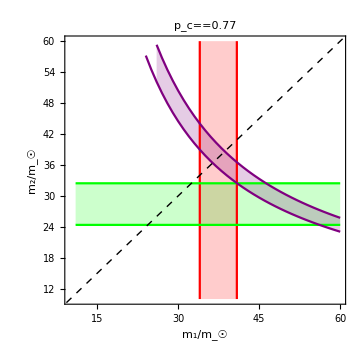

```mathematica
m1s=Range[10,60,1];
m2s=Range[10,60,1];

order=0;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]

prob=0.0;
prob=0.7700;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

Select[tapes[n][n][[1]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]],
Select[tapes[n][n][[2]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,0]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Filling->{1->{2},3->{4},5->{6}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

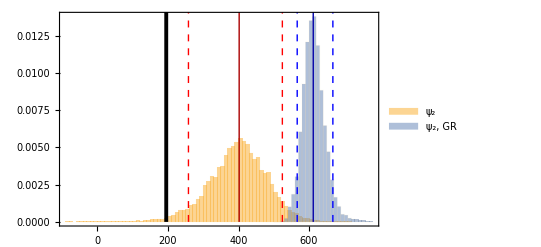

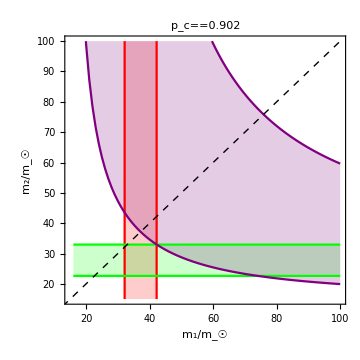

```mathematica
m1s=Range[15,100,1];
m2s=Range[15,100,1];

order=2;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]

prob=0.0;
prob=0.902;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{2,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]
(*Select[tapes[n][n][[2]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]]*)};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,2]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

```mathematica
1-0.902^3
```

0.266129

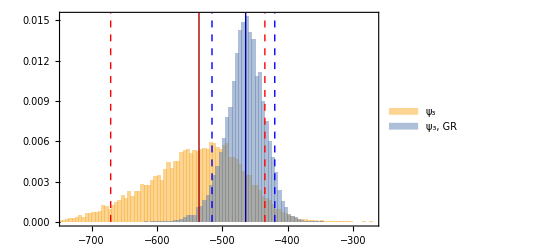

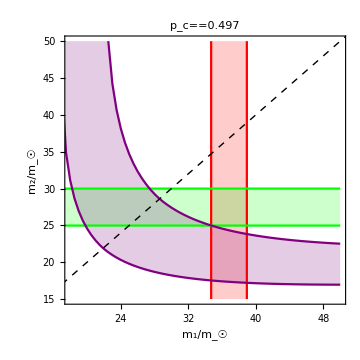

```mathematica
m1s=Range[15,50,1/2];
m2s=Range[15,50,1/2];

order=3;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]

prob=0.0;
prob=0.497;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{3,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,3]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,PlotRange->{{18,m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],
Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

-Graphics-

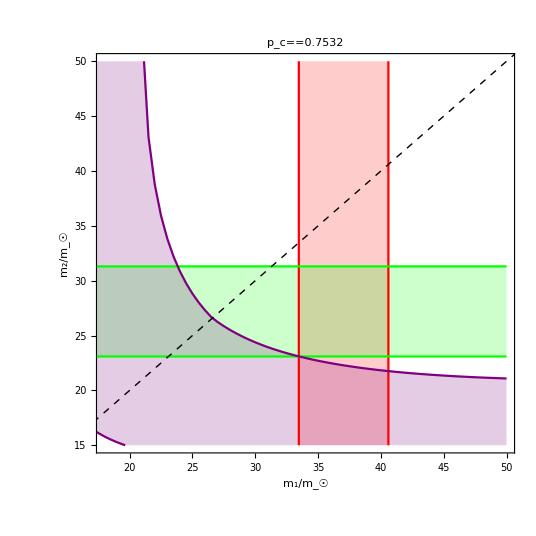

```mathematica
m1s=Range[15,50,1/2];
m2s=Range[15,50,1/2];

order=3;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]

prob=0.0;
(*11*)prob=0.3809;
(*12*)prob=0.44;
(*13*)prob=0.593;

(*21*)prob=0.435;
(*22*)prob=0.495;
(*23*)prob=0.64;

(*31*)prob=0.583;
(*22*)prob=0.633;
(*23*)prob=0.7532;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{3,BCI[n]["spin1z"][[3]],BCI[n]["spin2z"][[3]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,3]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,PlotRange->{{18,m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],
Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

```mathematica
1-0.495^3
```

0.878713

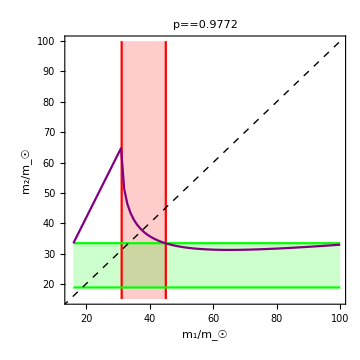

```mathematica
m1s=Range[15,100,1];
m2s=Range[15,100,1];

n="cpsi4";n1="psi0";n2="psi3";

prob=0.9772;
(*11*)prob=0.9778;
(*12*)prob=0.977588;
(*13*)prob=0.975481;

(*21*)prob=0.977587;
(*22*)prob=0.9772;
(*(*23*)prob=0.97489;

(*31*)prob=0.976036;
(*22*)prob=0.9754;
(*23*)prob=0.97352;*)

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{4,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

plots[n]=ListLinePlot[
{Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]},
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4}(*,5->{6}*)},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Black,Dashed,Line[{{0,0},{100,100}}],
(*最后绘制图例-优先级最高*)Inset[
Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,4]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left],
Background->White],Scaled[{0.3,0.8}],{0,0}]},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[p==value]]],
ImageSize->Medium]
```

```mathematica
1-0.9772^3
```

0.0668523

```mathematica
(*m1s=Range[15,60,1];
m2s=Range[15,60,1];

n="cpsi4";n1="psi0";n2="psi3";
prob1=0.9772;
(*再大一点会扫过这个矩形*)
prob2=0.989;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];
pInterval[n]=Join[IntervalFromProbability[prob2],IntervalFromProbability[prob1]];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{4,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s,{tapeIntervals["mass1"][[3]],#}&/@m2s,{tapeIntervals["mass1"][[4]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s,{#,tapeIntervals["mass2"][[3]]}&/@m1s,{#,tapeIntervals["mass2"][[4]]}&/@m1s};

plots[n]=ListLinePlot[
{tapes[n]["mass1"][[1]][[2;;]],
tapes[n]["mass1"][[2]][[2;;]],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

(*tapes[n][n][[1]][[2;;]],*)
(*Select[tapes[n][n][[2]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]],*)
Join[Reverse/@Select[tapes[n][n][[2]][[2;;]],#[[1]]>=#[[2]]&],Select[tapes[n][n][[2]][[2;;]],#[[1]]>=#[[2]]&]],

tapes[n]["mass1"][[3]][[2;;]],
tapes[n]["mass1"][[4]][[2;;]],
tapes[n]["mass2"][[3]][[2;;]],
tapes[n]["mass2"][[4]][[2;;]],
(*Select[tapes[n][n][[4]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]]*)
Join[Reverse/@Select[tapes[n][n][[4]][[2;;]],#[[1]]>=#[[2]]&],Select[tapes[n][n][[4]][[2;;]],#[[1]]>=#[[2]]&]]
},
PlotStyle->{
Directive[Red,Dashed,AbsoluteThickness[1.0]],
Directive[Red,Dashed,AbsoluteThickness[1.0]],
Directive[Green,Dashed,AbsoluteThickness[1.0]],
Directive[Green,Dashed,AbsoluteThickness[1.0]],
Directive[Purple,Dashed],
Red,Red,Green,Green,Purple,Purple
},

Filling->{
(*1->{2},3->{4},*)
(*6->{7},8->{9},*)
5->{10}},
FillingStyle->{HatchFilling["Diagonal"]},
AspectRatio->1,
PlotRange->{{0.965*m1s[[1]],m1s[[-1]]},{m2s[[1]],1.015*m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Black,Dashed,Line[{{0,0},{100,100}}],
Inset[
Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,4]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left](*,
Background->White*)
],
Scaled[{0.3,0.8}],
{0,0}
]
},
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
AxesLabel->{TraditionalForm[Subscript[m,1]/Subscript[m,"☉"]],TraditionalForm[Subscript[m,2]/Subscript[m,"☉"]]},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[p==value]]],
ImageSize->Medium]*)
```

-Graphics-

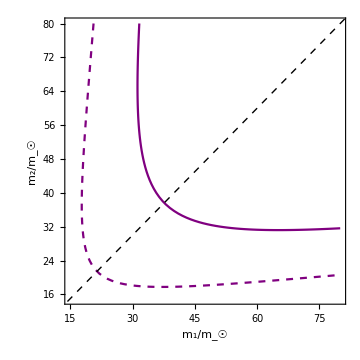

```mathematica
m1s=Range[15,80,1];
m2s=Range[15,80,1];

order=4;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]

prob1=0.9772;
(*再大一点会扫过这个矩形*)
prob2=0.989;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];
pInterval[n]=Join[IntervalFromProbability[prob2],IntervalFromProbability[prob1]];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m1s},{2},
{4,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
Join[Reverse[Reverse/@Select[tapes[n][n][[2]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[2]][[2;;]],#[[1]]>=#[[2]]&]],
Join[Reverse[Reverse/@Select[tapes[n][n][[4]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[4]][[2;;]],#[[1]]>=#[[2]]&]]
(*tapes[n][n][[2]][[2;;]],
tapes[n][n][[4]][[2;;]]*)
};
legends[n]=Panel[
Column[{
LineLegend[{Directive[Purple,Dashed],Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[ψ,4],", ",With[{value=prob1},TraditionalForm[HoldForm[p==value]]]}]],
TraditionalForm[Row[{Subscript[ψ,4],", ",With[{value=prob2},TraditionalForm[HoldForm[p==value]]]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left](*,
Background->White*)
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{
Directive[Purple,Dashed],
Purple
},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{
(*1->{2},3->{4},*)
(*6->{7},8->{9},*)
5->{10}},
FillingStyle->{HatchFilling["Diagonal"]},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],1m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Black,Dashed,Line[{{0,0},{100,100}}],
Inset[
legends[n],
Scaled[{0.3,0.8}],
{0,0}
]
},
(*PlotLabel->With[{value=prob},TraditionalForm[HoldForm[p==value]]],*)
ImageSize->Medium]
```

```mathematica
1-0.925^3
```

0.208547

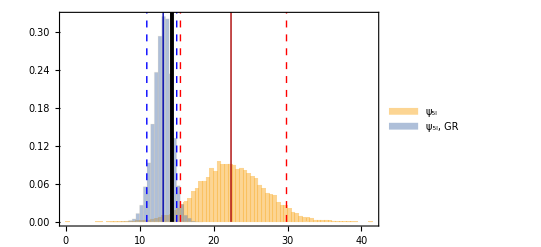

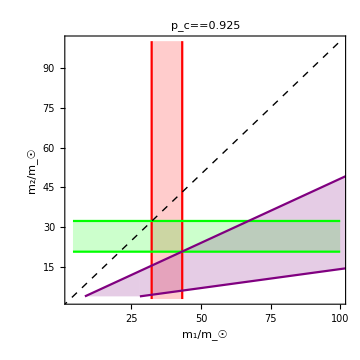

```mathematica
m1s=Range[3,100,1];
m2s=Range[3,100,1];

order="5l";
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]

prob=0.05;
prob=0.925;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

Reverse/@tapes[n][n][[1]][[2;;]],
Reverse/@tapes[n][n][[2]][[2;;]],
{(Reverse/@tapes[n][n][[1]][[2;;]])[[1]],(Reverse/@tapes[n][n][[2]][[2;;]])[[1]]}(* 补上紫线左边的阴影区 *)
};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,"5l"]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],

PlotStyle->{Red,Red,Green,Green,Purple,Purple,Transparent},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6},5->{7}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

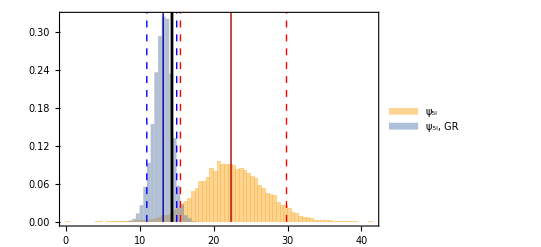

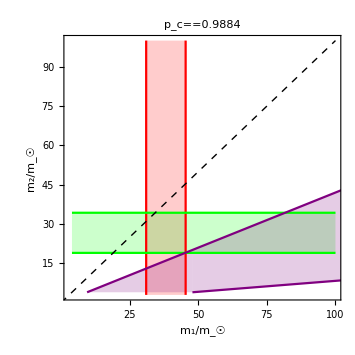

```mathematica
m1s=Range[3,100,1];
m2s=Range[3,100,1];

order="5l";
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]

prob=0.05;
(*11*)prob=0.8648;
(*12*)prob=0.8907;
(*13*)prob=0.9408;

(*21*)prob=0.9049;
(*22*)prob=0.925;
(*23*)prob=0.9593;

(*31*)prob=0.9669;
(*22*)prob=0.9748;
(*23*)prob=0.9884;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[3]],BCI[n]["spin2z"][[3]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

Reverse/@tapes[n][n][[1]][[2;;]],
Reverse/@tapes[n][n][[2]][[2;;]],
{(Reverse/@tapes[n][n][[1]][[2;;]])[[1]],(Reverse/@tapes[n][n][[2]][[2;;]])[[1]]}(* 补上紫线左边的阴影区 *)
};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,"5l"]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],

PlotStyle->{Red,Red,Green,Green,Purple,Purple,Transparent},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6},5->{7}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

```mathematica
BCI[n][n]
```

{15.522,22.3624,29.8634}

```mathematica
1-0.925^3
```

0.208547

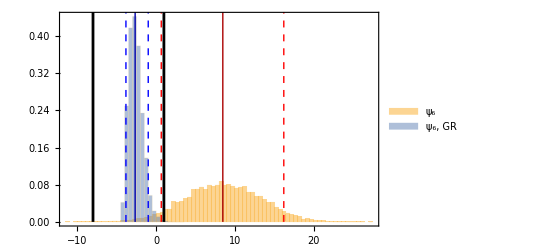

-Graphics-

```mathematica
m1s=Range[15,80,1];
m2s=Range[15,80,1];

order=6;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]


prob=0.97676;
prob=0.98634;

(*11*)prob=0.987457;
(*12*)prob=0.983655;
(*(*13*)prob=0.965;*)

(*21*)prob=0.9825;
(*22*)prob=0.976758;
(*(*23*)prob=0.9593;*)

(*(*31*)prob=0.95;*)
(*(*22*)prob=0.97;*)
(*(*23*)prob=0.9475;*)

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{6,BCI[n]["spin1z"][[3]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

plots[n]=ListLinePlot[
{Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

tapes[n][n][[1]][[2;;]](*,
tapes[n][n][[2]][[2;;]]*)},
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4}(*,5->{6}*)},
FillingStyle->{HatchFilling["Diagonal"]},AxesLabel->{TraditionalForm[Subscript[m,1]/Subscript[m,"☉"]],TraditionalForm[Subscript[m,2]/Subscript[m,"☉"]]},AspectRatio->1,
PlotRange->{{0.96*m1s[[1]],m1s[[-1]]},{m2s[[1]],1.015*m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Black,Dashed,Line[{{0,0},{100,100}}],
(*最后绘制图例-优先级最高*)Inset[
Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,6]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left],
Background->White],Scaled[{0.3,0.8}],{0,0}]},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[p==value]]],
ImageSize->Medium]
```

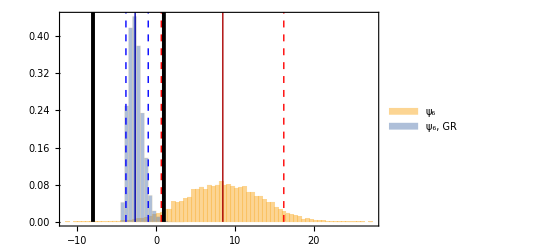

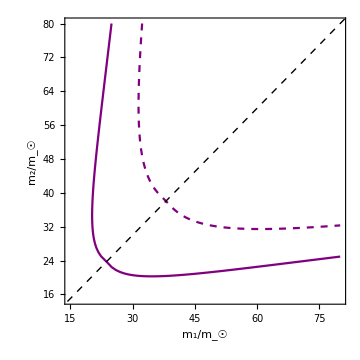

```mathematica
m1s=Range[15,80,1];
m2s=Range[15,80,1];

order=6;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]


prob1=0.97676;
(*再大一点会扫过这个矩形*)
prob2=0.98634;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];
pInterval[n]=Join[IntervalFromProbability[prob2],IntervalFromProbability[prob1]];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m1s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
Join[Reverse[Reverse/@Select[tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&]],
Join[Reverse[Reverse/@Select[tapes[n][n][[3]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[3]][[2;;]],#[[1]]>=#[[2]]&]]
(*tapes[n][n][[1]][[2;;]],
tapes[n][n][[3]][[2;;]]*)
};
legends[n]=Panel[
Column[{
LineLegend[{Directive[Purple,Dashed],Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[ψ,6],", ",With[{value=prob1},TraditionalForm[HoldForm[p==value]]]}]],
TraditionalForm[Row[{Subscript[ψ,6],", ",With[{value=prob2},TraditionalForm[HoldForm[p==value]]]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left](*,
Background->White*)
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{
Directive[Purple,Dashed],
Purple
},

Axes->True,
Frame->True,
FrameTicks->True,
Filling->{
(*1->{2},3->{4},*)
(*6->{7},8->{9},*)
5->{10}},
FillingStyle->{HatchFilling["Diagonal"]},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],1m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Black,Dashed,Line[{{0,0},{100,100}}],
Inset[
legends[n],
Scaled[{0.3,0.8}],
{0,0}
]
},
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
AxesLabel->{TraditionalForm[Subscript[m,1]/Subscript[m,"☉"]],TraditionalForm[Subscript[m,2]/Subscript[m,"☉"]]},
(*PlotLabel->With[{value=prob},TraditionalForm[HoldForm[p==value]]],*)
ImageSize->Medium]
```

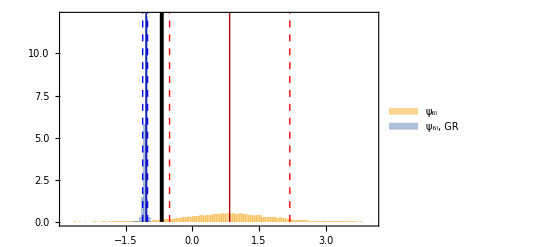

-Graphics-

```mathematica
m1s=Range[15,60,1];
m2s=Range[15,60,1];

order="6l";
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]


prob=0.8727;
(*prob=0.95;*)

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

plots[n]=ListLinePlot[
{Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]},
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6}},
FillingStyle->{HatchFilling["Diagonal"]},AxesLabel->{TraditionalForm[Subscript[m,1]/Subscript[m,"☉"]],TraditionalForm[Subscript[m,2]/Subscript[m,"☉"]]},AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],60}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Black,Dashed,Line[{{0,0},{100,100}}],
(*最后绘制图例-优先级最高*)Inset[
Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,"6l"]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left],
Background->White],Scaled[{0.3,0.8}],{0,0}]},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[p==value]]],
ImageSize->Medium]
```

-Graphics-

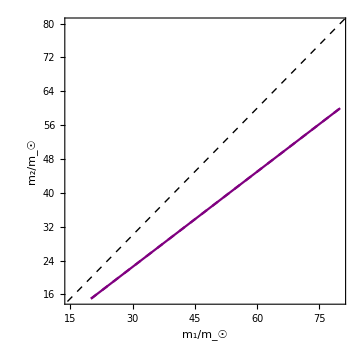

```mathematica
m1s=Range[15,80,1];
m2s=Range[15,80,1];

order="6l";
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]


prob1=0.8727;
(*再大一点会扫过这个矩形*)
prob2=0.95;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];
pInterval[n]=Join[IntervalFromProbability[prob2],IntervalFromProbability[prob1]];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m1s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[Reverse[Reverse/@Select[tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&]],
Join[Reverse[Reverse/@Select[tapes[n][n][[3]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[3]][[2;;]],#[[1]]>=#[[2]]&]]*)
tapes[n][n][[1]][[2;;]],
tapes[n][n][[3]][[2;;]]
};
legends[n]=Panel[
Column[{
LineLegend[{Directive[Purple,Dashed],Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[ψ,6],", ",With[{value=prob1},TraditionalForm[HoldForm[p==value]]]}]],
TraditionalForm[Row[{Subscript[ψ,6],", ",With[{value=prob2},TraditionalForm[HoldForm[p==value]]]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left](*,
Background->White*)
];

patch6=ListLinePlot[
{
(*Join[Reverse[Reverse/@Select[tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&]],
Join[Reverse[Reverse/@Select[tapes[n][n][[3]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[3]][[2;;]],#[[1]]>=#[[2]]&]]*)
tapes[n][n][[1]][[2;;]],
tapes[n][n][[3]][[2;;]]
},
PlotStyle->{
Directive[Purple,Dashed],
Purple
},

Filling->{
(*1->{2},3->{4},*)
(*6->{7},8->{9},*)
5->{10}},
FillingStyle->{HatchFilling["Diagonal"]},
AspectRatio->1,
PlotRange->{{40.02,40.026},{30.015,30.020}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Black,Dashed,Line[{{0,0},{100,100}}]
},
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
(*PlotLabel->With[{value=prob},TraditionalForm[HoldForm[p==value]]],*)
ImageSize->Medium];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{
Directive[Purple,Dashed],
Purple
},

Axes->True,
Frame->True,
FrameTicks->True,
Filling->{
(*1->{2},3->{4},*)
(*6->{7},8->{9},*)
5->{10}},
FillingStyle->{HatchFilling["Diagonal"]},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],1m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],
Scaled[{0.3,0.8}],
{0,0}
],
Black,Dashed,Line[{{0,0},{100,100}}](*,
Inset[
patch6]*)
},
(*PlotLabel->With[{value=prob},TraditionalForm[HoldForm[p==value]]],*)
ImageSize->Medium]
```

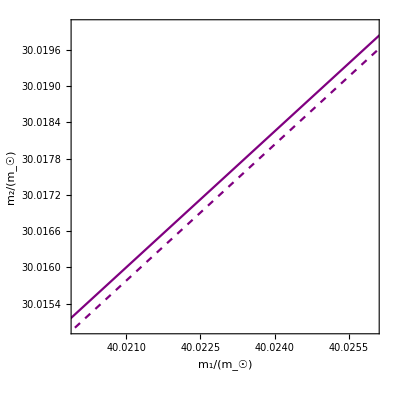

```mathematica
patch6
```

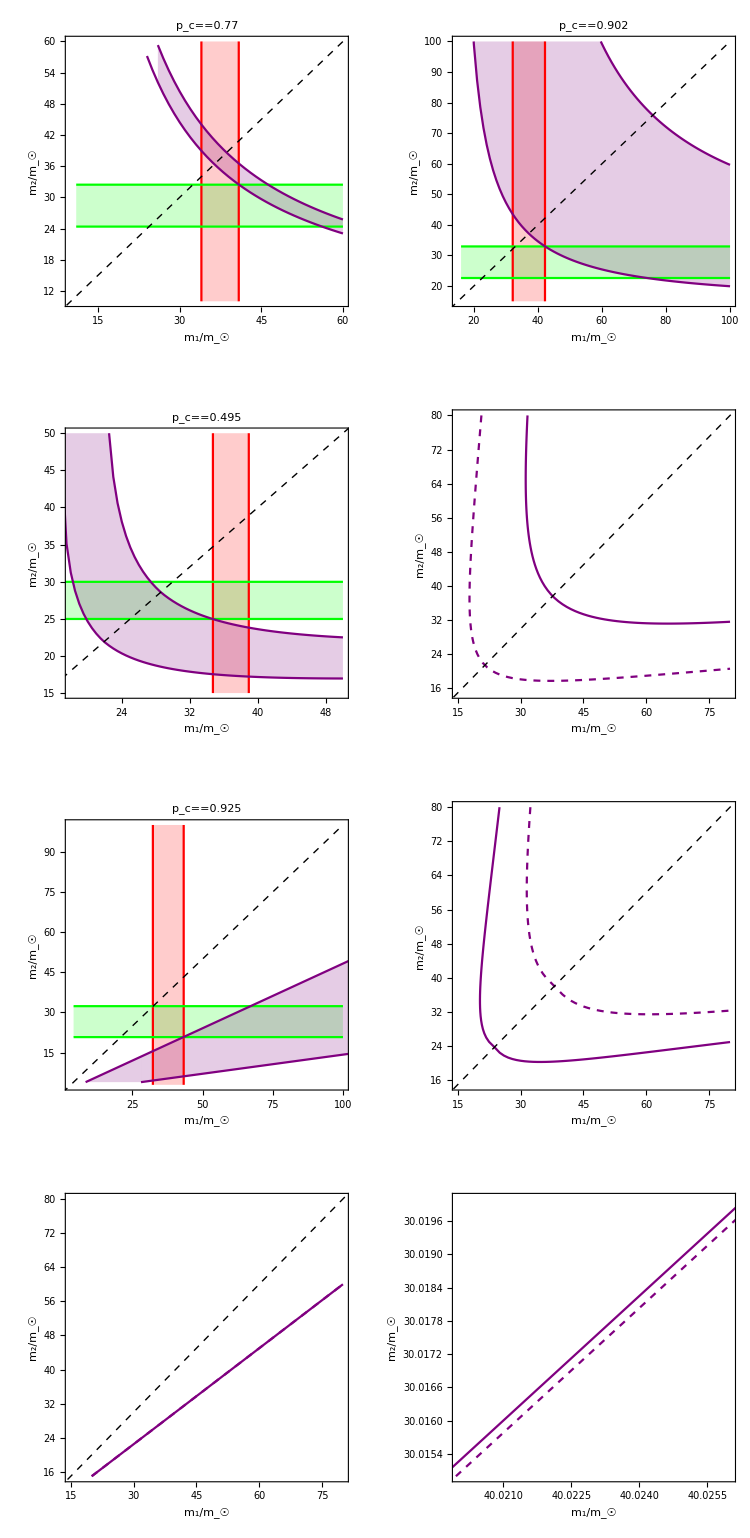

```mathematica
combinedPlot=GraphicsGrid[
Append[Partition[Values[plots],2],{plots[[7]],patch6}],(*将1维数组拆分为3×3的二维网格*)
(*Frame->All,*)(*给每个子图加边框，清晰分隔*)
(*Spacings->{15,15},*)(*控制子图间的水平/垂直间距（像素）*)
ImageSize->750,(*控制整个大图的总尺寸*)
PlotLabel->Style["3×3组合大图",16,Bold]  (*给整个大图加总标题*)]
```

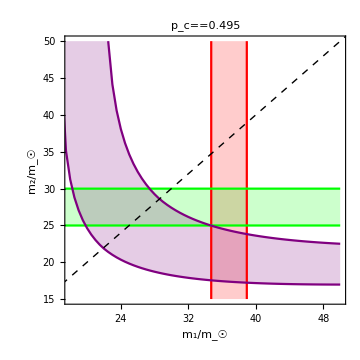
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Values[plots[[{1,3,5,6}]]]
```

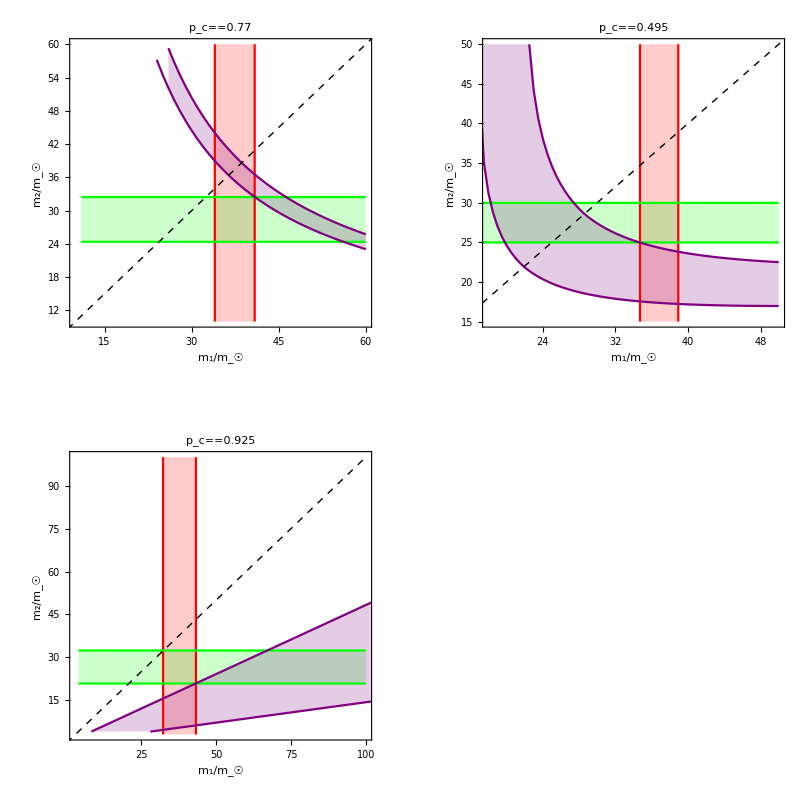

```mathematica
combinedPlot=GraphicsGrid[
Append[Partition[Values[plots[[{1,3}]]],2],{plots[[5]],}],(*将1维数组拆分为3×3的二维网格*)
(*Frame->All,*)(*给每个子图加边框，清晰分隔*)
(*Spacings->{15,15},*)(*控制子图间的水平/垂直间距（像素）*)
ImageSize->800,(*控制整个大图的总尺寸*)
PlotLabel->Style["3×3组合大图",16,Bold]  (*给整个大图加总标题*)]
```

```mathematica
Append[Values[plots[[{1,3}]]],{plots[[5]],}]
```

{-Graphics-,-Graphics-,{-Graphics-,Null}}

```mathematica
combinedPlot=GraphicsGrid[
Append[Partition[Values[plots],2],{plots[[7]],patch6}],(*将1维数组拆分为3×3的二维网格*)
(*Frame->All,*)(*给每个子图加边框，清晰分隔*)
(*Spacings->{15,15},*)(*控制子图间的水平/垂直间距（像素）*)
ImageSize->750,(*控制整个大图的总尺寸*)
PlotLabel->Style["3×3组合大图",16,Bold]  (*给整个大图加总标题*)]
```

-Graphics-

## Value Domains

```mathematica
vd=<||>;
```

```mathematica
(BCI["cpsi0"]["cpsi0"][[3]]-BCI["cpsi0"]["cpsi0"][[1]])/5000
vd["cpsi0"]=Manipulate[
Plot3D[
Function[{m1,m2},Psi[0,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi0"]["mass1"][[1]],BCI["cpsi0"]["mass1"][[3]]},
{m2,BCI["cpsi0"]["mass2"][[1]],BCI["cpsi0"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False,
AxesLabel->{TraditionalForm[Subscript[m,1]/Subscript[m,"☉"]],TraditionalForm[Subscript[m,2]/Subscript[m,"☉"]],TraditionalForm[Subscript[ψ,0]]}
],
{spin1z,BCI["cpsi0"]["spin1z"][[2]]},{spin2z,BCI["cpsi0"]["spin2z"][[2]]}
]
```

0.206569

```mathematica
(BCI["cpsi2"]["cpsi2"][[3]]-BCI["cpsi2"]["cpsi2"][[1]])/250
vd["cpsi0"]=Manipulate[
Plot3D[
Function[{m1,m2},Psi[2,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi2"]["mass1"][[1]],BCI["cpsi2"]["mass1"][[3]]},
{m2,BCI["cpsi2"]["mass2"][[1]],BCI["cpsi2"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi2"]["spin1z"][[2]]},{spin2z,BCI["cpsi2"]["spin2z"][[2]]}
]
```

1.06474

```mathematica
(BCI["cpsi3"]["cpsi3"][[3]]-BCI["cpsi3"]["cpsi3"][[1]])/150
Manipulate[
Plot3D[
Function[{m1,m2},Psi[3,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi3"]["mass1"][[1]],BCI["cpsi3"]["mass1"][[3]]},
{m2,BCI["cpsi3"]["mass2"][[1]],BCI["cpsi3"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi3"]["spin1z"][[2]]},{spin2z,BCI["cpsi3"]["spin2z"][[2]]}
]
```

1.57419

```mathematica
(BCI["cpsi4"]["cpsi4"][[3]]-BCI["cpsi4"]["cpsi4"][[1]])/5
Manipulate[
Plot3D[
Function[{m1,m2},Psi[4,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi4"]["mass1"][[1]],BCI["cpsi4"]["mass1"][[3]]},
{m2,BCI["cpsi4"]["mass2"][[1]],BCI["cpsi4"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi4"]["spin1z"][[2]]},{spin2z,BCI["cpsi4"]["spin2z"][[2]]}
]
```

23.7613

```mathematica
(BCI["cpsi5l"]["cpsi5l"][[3]]-BCI["cpsi5l"]["cpsi5l"][[1]])/1.5
Manipulate[
Plot3D[
Function[{m1,m2},Psi["5l",η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi5l"]["mass1"][[1]],BCI["cpsi5l"]["mass1"][[3]]},
{m2,BCI["cpsi5l"]["mass2"][[1]],BCI["cpsi5l"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi5l"]["spin1z"][[2]]},{spin2z,BCI["cpsi5l"]["spin2z"][[2]]}
]
```

9.56092

```mathematica
Manipulate[
Plot3D[
Function[{m1,m2},Psi["5l",η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,3,100},
{m2,3,100},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi5l"]["spin1z"][[2]]},{spin2z,BCI["cpsi5l"]["spin2z"][[2]]}
]
```

```mathematica
(BCI["cpsi6"]["cpsi6"][[3]]-BCI["cpsi6"]["cpsi6"][[1]])/0.5
Manipulate[
Plot3D[
Function[{m1,m2},Psi[6,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi6"]["mass1"][[1]],BCI["cpsi6"]["mass1"][[3]]},
{m2,BCI["cpsi6"]["mass2"][[1]],BCI["cpsi6"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi6"]["spin1z"][[2]]},{spin2z,BCI["cpsi6"]["spin2z"][[2]]}
]
```

31.1398

```mathematica
(BCI["cpsi6l"]["cpsi6l"][[3]]-BCI["cpsi6l"]["cpsi6l"][[1]])/0.1
Manipulate[
Plot3D[
Function[{m1,m2},Psi["6l",η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi6l"]["mass1"][[1]],BCI["cpsi6l"]["mass1"][[3]]},
{m2,BCI["cpsi6l"]["mass2"][[1]],BCI["cpsi6l"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi6l"]["spin1z"][[2]]},{spin2z,BCI["cpsi6l"]["spin2z"][[2]]}
]
```

27.0383

```mathematica
(*Manipulate[
Plot3D[
Function[{m1,m2},Psi[7,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,20,80},
{m2,20,80},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,0.06070798549182338},{spin2z,0.09392835788044217}
(*{spin1z,-1,1},{spin2z,-1,1}*)
]*)
```

## Exports

```mathematica
Do[
name=deviationNames[[i]];
exportPath=StringJoin["D:/Documents/workspace/课题/论文/figs/GW150914/comp_plots/","GW150914_inverse_plot_",
name,
".pdf"];
Export[exportPath,compPlots[name],"PDF",ImageResolution->1000],
{i,1,Length[deviationNames]}]
```

```mathematica
Do[
name=deviationNames[[i]];
exportPath=StringJoin["D:/Documents/workspace/课题/论文/figs/GW150914/inverse_plots/","GW150914_inverse_plot_",
name,
".pdf"];
Export[exportPath,plots[name],"PDF",ImageResolution->1000],
{i,1,Length[deviationNames]}]
```

```mathematica
Export["D:/Documents/workspace/课题/论文/figs/GW150914/inverse_plots/GW150914_patch_cpsi6.pdf",patch6,"PDF",ImageResolution->1000]
```

D:/Documents/workspace/课题/论文/figs/GW150914/inverse_plots/GW150914_patch_cpsi6.pdf

```mathematica
Do[
name=deviationNames[[i]];
exportPath=StringJoin["D:/Documents/workspace/课题/论文/figs/GW150914/value_domains/","GW150914_vd_",
name,
".pdf"];
Export[exportPath,vd[name],"PDF",ImageResolution->1000],
{i,1,Length[deviationNames]}]
```